```mathematica
ϵ[m_]=If[m==0, -s kappa, Sign[m]Sqrt[Abs[m]+ kappa^2]];
alpha[m_]=(-Sqrt[Abs[m]])/(ϵ[m] s - kappa);
xi=((alpha[m]^2+1)(alpha[n]^2+1))^(-1)/(ϵ[m]-ϵ[n])^2; (*Nb defined without heaviside *)
```

```mathematica
Integrate[
xi (ϵ[m] + ϵ[n]) alpha[m]^2/.{n->0, m->1,s->1},
{kappa,  0, Infinity}
]
```

1/4

```mathematica
Table[
Integrate[
xi (ϵ[m] + ϵ[n]) alpha[m]^2/.{n->-i, m->i+1,s->1},
{kappa,  -Infinity, Infinity}
],
{i, 1,2}
]
```

```mathematica
FullSimplify[xi (ϵ[m] + ϵ[n]) alpha[m]^2/.s->1, {m>0, n<0, {m,n}∈Reals}]
```

(m (√(kappa^2+m)-√(kappa^2+Abs[n])) (kappa+√(kappa^2+Abs[n]))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2+Abs[n]))^2 (Abs[n]+kappa (kappa+√(kappa^2+Abs[n]))))

```mathematica
Integrate[
(m (√(kappa^2+m)-√(kappa^2-n)) (kappa+√(kappa^2-n))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2-n))^2 (-n+kappa (kappa+√(kappa^2-n)))),
{kappa, -Infinity, Infinity},
Assumptions->{{m,n}∈Integers, m>0, n<0}
]
```

(m^2-n^2+2 m n Log[-m/n])/(4 (m+n)^2)

```mathematica
%/.{m->i+1, n->-i}
```

1/4 (-i^2+(1+i)^2-2 i (1+i) Log[(1+i)/i])

```mathematica
Simplify[%]
```

1/4 (1+2 i-2 i (1+i) Log[1+1/i])

```mathematica
Sum[1/4 (1+2 i-2 i (1+i) Log[1+1/i]), {i, N}]
```

1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Zeta^(1,0)[-2,1+N]-6 Zeta^(1,0)[-2,2+N]+6 Zeta^(1,0)[-1,1+N]+6 Zeta^(1,0)[-1,2+N])

```mathematica
TraditionalForm[1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])]
```

```mathematica
1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])+1/4
```

```mathematica
Plot[1/4+1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N]),
{N, 2,4}
]
```

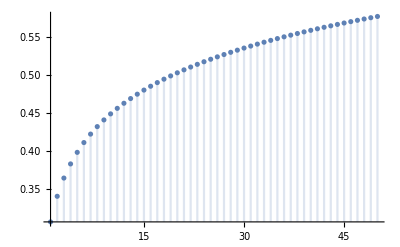

```mathematica
DiscretePlot[
1/4+1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])/.N->k
,{k,1,50}]
```

```mathematica
TeXForm[%]
```

\frac{1}{12} \left(6 \zeta ^{(1,0)}(-2,N+1)-6
   \zeta ^{(1,0)}(-2,N+2)+6 \zeta
   ^{(1,0)}(-1,N+1)+6 \zeta
   ^{(1,0)}(-1,N+2)+12 \log (A)+3 N^2+6
   N-1\right)

```mathematica
TraditionalForm[1/4 (1+2 i-2 i (1+i) Log[1+1/i])]
```

1/4 (2 i-2 (i+1) i log(1/i+1)+1)

```mathematica
1/4 (1+2 i-2 i (1+i) Log[1+1/i])/.i->1
```

1/4 (3-4 Log[2])

```mathematica
FullSimplify[(1+2 i-2 i (1+i) Log[1+1/i]), Assumptions->i∈PositiveIntegers]
```

1+2 i-2 i (1+i) Log[1+1/i]

```mathematica
Sum[(1+2 i-2 i (1+i) Log[1+1/i]), {i, 1,N}, Assumptions->i∈PositiveReals]
```

1/3 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Zeta^(1,0)[-2,1+N]-6 Zeta^(1,0)[-2,2+N]+6 Zeta^(1,0)[-1,1+N]+6 Zeta^(1,0)[-1,2+N])

```mathematica
Simplify[%%]
```

1-2 (-1+Log[1/i]) i-2 (1+Log[1/i]) i^2-i^3+O[i]^4

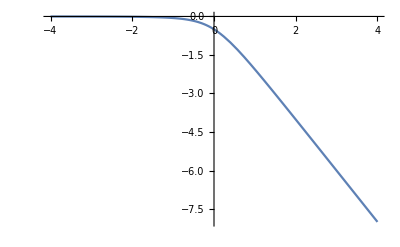

```mathematica
Plot[
xi (ϵ[m] + ϵ[n]) alpha[m]^2/.{n->0, m->-1, s->1},
{kappa, -4,4}
]
```